#### TO DO : at the beginning y(0)=0 so the system evolves toward the smallest non neg root/fp

Actually, the second solution would just gives a off result over the whole plane, which is not physically relevant.

#### 2) Computation for negative-weighted neuron (1st method using discriminant)

```mathematica
ClearAll[f,poly,w1p,w1n,x1p,x1n,δ,ks,b,y,fOFF];

(*the total sum of inputs reads as P-N (N is defined st the minus is in prefactor)*)

ks=0.02;
b=0.005;
δ=0.1;
(*this is the governing equation, i.e., the steady state equation for y (meaning that we've reached classification), whose contour (f(y)=0) give the separation btw off and on phases*)
f[y_]:=y (ks+y)-(1+y) (ks+y)*δ*y+(1+y) (ks+y)*0.017*x1p-y*(1+y) *(b+0.017*x1n);
```

```mathematica
poly=Expand[f[y]];
poly//TraditionalForm
```

-0.017 x1n y^2-0.017 x1n y+0.017 x1p y^2+0.01734 x1p y+0.00034 x1p-0.1 y^3+0.893 y^2+0.013 y

```mathematica
(*Δ=0 means there is a change of nature in the solution, e.g. we go from 3 solutions to 1 solution. This is a switch of activation of the neuron, delimitating the 2 phases*)
disc=FullSimplify[Discriminant[poly,y]];
Print["The discriminant of the y polynomial is Δ = ",disc];
```

The discriminant of the y polynomial is Δ = 0.000135648+8.3521×10^-8 x1n^4+x1n^3 (-0.0000108676-3.30743×10^-7 x1p)+x1n^2 (0.00024844+(0.0000318443+4.91137×10^-7 x1p) x1p)+x1n (-0.000361051+x1p (-0.00044181+(-0.0000310883-3.24128×10^-7 x1p) x1p))+x1p (-0.000607421+x1p (0.000193247+(0.0000101115+8.02136×10^-8 x1p) x1p))

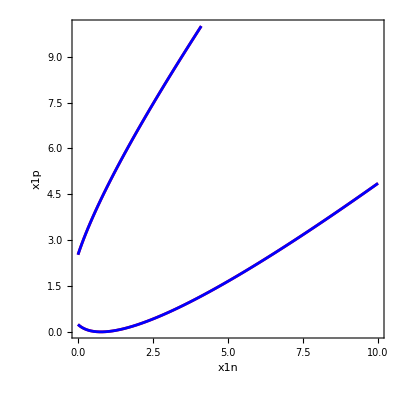

```mathematica
disctayl=Normal[Series[disc,{x1p,0,4},{x1n,0,4}]];

(*Plot the zero-contours of disc and its series expansion disctayl.Both curves are now in terms of x1n and x1p.*)
ContourPlot[Evaluate[{disc==0,disctayl==0}],{x1n,0,10},{x1p,0,10},ContourShading->None,ContourStyle->{Red,Blue},PlotPoints->50,FrameLabel->{"x1n","x1p"}]
```

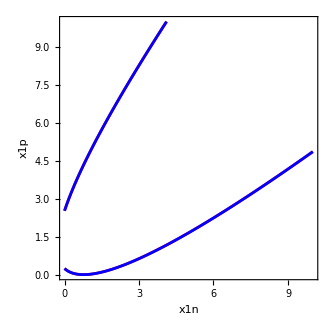

#### TO DO: try to plot the bifurcation point y(P,N) c’est moins facile c’est en 3d + EST CE QUE CONCENTRATIONS NEGATIVES SECONDES BRANCHES. CA VEUT BIEN DIRE QUE PAS VRAIE PHYSIQUEMEBT. EST CE QUON PEUT RAJOUTER DU BRUITS ET POINTS MAL IDENTIF2ES

The presence of the 2 branches is explained by the dual possibility to transient from 1s to 3s to 1s (ie switch on/off or off/on), depending on initial concentrations of N and P, i.e. starting from the upper or from the lower of the yellow strip. The two branches separate the parameter plane into regions with different numbers of equilibrium solutions. For example, one region might have three equilibria (e.g., two stable and one unstable), while another might have only a single equilibrium. The two branches act as boundaries between these regions. D’un autre côté, si on part initialement de hautes concentrations en N et P (N>P sur le diagramme de bifurcation), on est dans le OFF state et on traverse la branche jaune dans l’autre sens.

 fgfb

```mathematica
-Graphics--Graphics--Graphics-
```

-Graphics-

-Graphics-
Bref quoi qu’il en soit, on a deux branches puisqu’il y a deux moyens d’arriver à un OFF state en partant d’un ON state : soit en augmentant P, soit en baissant N.

Starting anywhere below the 1st branch (OFF) ie for low starting values of N and P (as expected in the experiments), and increasing the P value, we undergo a sp bifurcation, then a bistability, then a second sp bifurcation, to finally end up in the ON phase.

```mathematica
-Graphics--Graphics-
```

But we can also start anywhere below the second branch, with fairly high values of N (OFF phase). Then decreasing N, we undergo a switch from OFF to sn bifurcation, to bi stability, to a second bifurcation, then finally to a the ON phase. Yet, this solution is not explored here, as it requires directly at the beginning  very high concentrations of N and P inputs.

```mathematica
-Graphics--Graphics--Graphics-
```

New, c’est probablement bien une histoire de conditions initiales, si on par de off, zone violette tout en bas et qu’on augmente x1p à x1n fixé, aucune raison que d’un coup ça devienne off

Here are some ways to interpret these two branches:

Different Bifurcation Scenarios:
Each branch represents a distinct “bifurcation boundary.” For a given branch, as you vary the parameters across it, the number of steady‑state solutions of f(y)=0 changes. One branch may signal the onset where two roots merge and vanish (or appear), while the other branch represents a different bifurcation scenario.

Regions in Parameter Space:
The two branches separate the parameter plane into regions with different numbers of equilibrium solutions. For example, one region might have three equilibria (e.g., two stable and one unstable), while another might have only a single equilibrium. The two branches act as boundaries between these regions.

Upper and Lower Limits for Activation:
If your system has a meaning such as a “switch” (for example, corresponding to an activation or classification threshold), then the two branches might be interpreted as the lower and upper thresholds. Crossing one branch might represent activating the system (turning “on”), and crossing the other branch might represent deactivating it (turning “off”), depending on your system’s dynamics.

Multiple Conditions on the Degeneracy:
Algebraically, two distinct branches indicate that the equation obtained by eliminating y is not a single-valued function over the entire parameter space; rather, it has two “sheets” corresponding to two different solution families. Each family corresponds to a different way the double root condition is satisfied. In some cases (depending on additional criteria like stability or other system-specific constraints) one branch might be physically relevant while the other is not, or both might be significant in different contexts.

In summary:
The two branches in your graph mark two separate sets of conditions in the (x1n,x1p) space where the equilibrium becomes degenerate (i.e. a saddle‑node bifurcation occurs). They delineate changes in the qualitative behavior of the steady‑state solutions. How you interpret them further—for example, assigning physical meaning or stability—will depend on additional analysis of your system (such as computing eigenvalues or considering additional constraints from the model).

#### 3) Computation for negative-weighted neuron (2st method )

```mathematica
ClearAll[f,poly,x1p,x1n,y,δ,ks,b];

(*Define parameters*)
ks=0.02;
b=0.005;
δ=0.1;

(*Define the steady‑state equation f[y] (the governing equation)*)
f[y_]:=y (ks+y)-(1+y) (ks+y)*δ*y+(1+y) (ks+y)*0.017*x1p-y*(1+y)*(b+0.017*x1n);

(*Expand the polynomial in y for clarity*)
poly=Expand[f[y]];
poly//TraditionalForm
```

-0.017 x1n y^2-0.017 x1n y+0.017 x1p y^2+0.01734 x1p y+0.00034 x1p-0.1 y^3+0.893 y^2+0.013 y

A saddle-node)bifurcation occurs when a solution of the equation becomes degenerate, ie  when two (or more) roots merge. For a function f(y) , if a particular value y*​ is a double root then not only f(y*​)=0 but also f’(y*)=0

```mathematica
(*At a bifurcation (or "fold") point,f(y)=0 and the derivative with respect to y vanish. Instead of computing the full discriminant,we can solve:poly==0 and D[poly,y]==0 and then eliminate y to get a relation between x1n and x1p.*)
bifurcationSystem={poly==0,D[poly,y]==0};

(*Eliminate y to get a condition solely in x1n and x1p*)
bifurcationCondition=Eliminate[bifurcationSystem,y];
Print["Bifurcation condition: ",bifurcationCondition];
```

Bifurcation condition: 3.39119×10^11-9.02628×10^11 x1n+6.211×10^11 x1n^2-2.71689×10^10 x1n^3+2.08803×10^8 x1n^4-1.51855×10^12 x1p-1.10453×10^12 x1n x1p+7.96107×10^10 x1n^2 x1p-8.26858×10^8 x1n^3 x1p+4.83118×10^11 x1p^2-7.77206×10^10 x1n x1p^2+1.22784×10^9 x1n^2 x1p^2+2.52788×10^10 x1p^3-8.10321×10^8 x1n x1p^3+2.00534×10^8 x1p^4==0.

Simplified bifurcation condition: 1624.11+1. x1n^4+x1n^3 (-130.118-3.96 x1p)+x1n^2 (2974.58+x1p (381.273+5.8804 x1p))+x1n (-4322.88+x1p (-5289.81+(-372.221-3.8808 x1p) x1p))+x1p (-7272.67+x1p (2313.75+(121.066+0.9604 x1p) x1p))==0

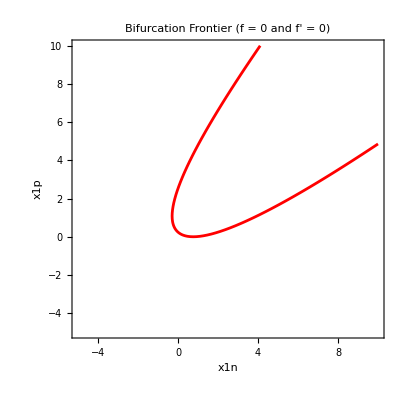

```mathematica
bifurcationConditionSimp=FullSimplify[bifurcationCondition];
Print["Simplified bifurcation condition: ",bifurcationConditionSimp];

(*Plot this bifurcation frontier (the set where the system undergoes a change in number of solutions)*)
ContourPlot[Evaluate[bifurcationConditionSimp],{x1n,-5,10},{x1p,-5,10},ContourStyle->{Red},ContourShading->None,PlotPoints->50,FrameLabel->{"x1n","x1p"},PlotLabel->"Bifurcation Frontier (f = 0 and f' = 0)"]
```

The 2 branches refer to two different bifurcation scenario